## Many Harmonic Oscillators

## Completed and Analyzed in class, February 21, 2025

This is the ninth notebook for you to complete.

### Many Oscillators — Formulas for the Accelerations

At the end of Coupled Harmonic Oscillators - Theory notebook, I hinted at where we were going to go next. For seven equal masses connected by eight identical springs, we had:

a_1=-ω_0^2 x_1+ω_0^2(x_2-x_1)

a_2=-ω_0^2(x_2-x_1)+ω_0^2(x_3-x_2)
 
...

a_6=-ω_0^2(x_6-x_5)+ω_0^2(x_7-x_6)

a_7=-ω_0^2(x_7-x_6)-ω_0^2 x_7

where

ω_0^2≡k/m

Also, why stop at 7? Let’s have n masses and n+1 springs, and for starters, I’ll have n=10.

```mathematica
omega0=2Pi; 
n=10;
```

### Many Oscillators — Implementing the Accelerations

It is most definitely not going to cut it to have to write out an equation for the acceleration of each of the n masses. We are going to have to do it more generally.

```mathematica
(* How about this? Actually, the next statement doesn't work, so it is commented out. *)
(* a[i,allxs_]:=-(allxs[i]-allxs[i-1])omega0^2+(allxs[i+1]-allxs[i])omega0^2 *)
(* It doesn't work, because the end ones have a slightly different formula. *)
(* So how about this, where the end ones have been treated specially? *)
a[k_,allxs_]:=-(allxs[[k]]-If[k==1, 0, allxs[[k-1]]])omega0^2+(If[k==n,0,allxs[[k+1]]]-allxs[[k]])omega0^2
```

### Initial Conditions

Let’s push the left mass to the left, and leave all the other masses at equilibrium. Let’s start all the masses with no velocity:

```mathematica
tInitial = 0.0;
tFinal = 60.0; 
initialXs = Table[If[k==1,-0.5,0.0],{k, n}];
initialVs = Table[0.0,n];
(* We have to decide how we are packing the time, the positions, and the *)
(* velocities into the initial conditions list, but here is the obvious choice: *)
initialConditions={tInitial,initialXs,initialVs};
```

### Second-Order Runge-Kutta — Formulas for n Particles

t_(i+1)=t_i+Δt

x_j^*=x_j(t_i)+v_j(t_i)·Δt/2       (j goes from 1 to n)

v_j(t_(i+1))=v_j(t_i)+a_j(all the x^*)·Δt

x_j(t_(i+1))=x_j(t_i)+ (v_j(t_i)+v_j(t_(i+1)))Δt/2

### Second-Order Runge-Kutta — Implementing the Formulas

```mathematica
steps = 12000;
deltaT = (tFinal - tInitial)/steps;

rungeKutta2[cc_]:= (
curTime=cc[[1]];
curxs=cc[[2]];
curvs=cc[[3]];
newTime=curTime+deltaT;
(* Now I have left you six equations to implement *)
xStars=Table[curxs[[j]]+curvs[[j]]deltaT/2,{j,n}];
newvs=Table[curvs[[j]]+a[j,xStars]deltaT,{j,n}];
newxs=Table[curxs[[j]]+(curvs[[j]]+newvs[[j]])deltaT/2,{j,n}];
{newTime,newxs,newvs}
)
(* Test your implementation on the initial conditions *)
N[rungeKutta2[initialConditions]]
(* Now this is what I get: *)
(* {0.005, {-0.499507,-0.00024674,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}, *)(* {0.197392,-0.098696,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}} *)
```

{0.005,{-0.499507,-0.00024674,0.,0.,0.,0.,0.,0.,0.,0.},{0.197392,-0.098696,0.,0.,0.,0.,0.,0.,0.,0.}}

#### Using NestList[] to Repeatedly Apply rungeKutta2[]

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];
```

#### Transposing to Get Points We Can Put in ListLinePlot[]

```mathematica
rk2ResultsTransposed=Transpose[rk2Results];
xs=rk2ResultsTransposed[[2]];
```

#### A Graphic

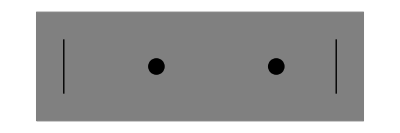

```mathematica
coupledOscillatorGraphic[xs_]:=Graphics[{
(* the first line makes a gray rectangle *)
{EdgeForm[Thin],Gray,Polygon[{{0,-1},{6,-1},{6,1},{0,1}}]},
Line[{{0.5,-0.5},{0.5,0.5}}],
Line[{{5.5,-0.5},{5.5,0.5}}],
Style[Point[{xs[[1]]+2,0}],PointSize[0.03]],
Style[Point[{xs[[2]]+4,0}],PointSize[0.03]]
}]
coupledOscillatorGraphic[{0.2, 0.4}]
```

#### Animating The Graphics

```mathematica
Animate[coupledOscillatorGraphic[xs[[i]]],{i,1,steps,1}, DefaultDuration->tFinal-tInitial]
```

#### Comparing With YouTube

YouTube could be a great reference, but it has filled up with such an amazing amount of garbage, that finding a good video of coupled harmonic oscillators was surprisingly hard. I finally found a whole page of demonstrations put together by Caltech: https://physicsdemos.caltech.edu/index_simple.html, and one of the demonstrations was of the situation that we have simulated:

https://youtu.be/Eoux0MsZqBY

Just watch the first little bit. Then, if we want to understand more of what is going on later in the video, we are going to have to put in a bit of damping and a driving force, but we have already done so much of the fundamental work in building up this notebook, that would not actually be very difficult.